## Бустинг

Бустинг представляет собой жадный алгоритм построения композиции базовых алгоритмов. Основная идея заключается в том, чтобы, имея множество относительно слабых алгоритмов обучения, построить их хорошую линейную комбинацию. Он похож на бэггинг тем, что базовый алгоритм фиксирован. Отличие состоит в том, что обучение базовых алгоритмов для композиции происходит итеративно, и каждый следующий алгоритм стремится компенсировать недостатки композиции всех предыдущих алгоритмов.

Общая схема бустинга:
	• Искомый ансамбль алгоритмов имеет вид a(x)=(∑_(t=1)^T α_t b_t(x)), где b_t – базовые алгоритмы.
	• Ансамбль строится итеративно, оптимизируя на каждом шаге функционал Q_t, равный количеству ошибок текущей композиции на обучающей выборке.
	• При добавлении слагаемого α_t b_t(x) в сумму, функционал Q_t оптимизируется только по базовому алгоритму b_t и коэффициенту α_t при нём, все предыдущие слагаемые считаются фиксированными.
	• Функционал Q_t имеет вид суммы по объектам обучающей выборки пороговых функций вида [y_i∑_(j=1)^t α_j b_j(x_j)<0], имеющих смысл «текущая композиция ошибается на объекте с номером i». Каждое такое слагаемое имеет вид «ступеньки» и является разрывной функцией. Для упрощения решения задачи оптимизации такая пороговая функция заменяется на непрерывно дифференцируемую оценку сверху. В итоге получается новый функционал (Q̂)_t≥Q_t, минимизация которого приводит к минимизации исходного функционала Q_t.

Используя различные аппроксимации для пороговой функции потерь [z<0], будем получать различные виды бустинга. Примеры:
• ⅇ^-z – AdaBoost
• log_2(1+ⅇ^-z) – LogitBoost
• (1-z)^2 – GentleBoost
• ⅇ^(-cz(z+a)) – BrownBoost

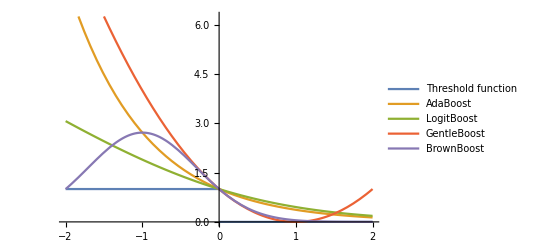

```mathematica
Plot[{Piecewise[{{1,z<0},{0,z≥0}}],ⅇ^-z,Log[2,1+ⅇ^-z],(1-z)^2,ⅇ^(-z(z+2))},{z,-2,2},PlotLegends->{"Threshold function","AdaBoost","LogitBoost","GentleBoost","BrownBoost"}]
```

### Алгоритм AdaBoost

• Инициализировать веса объектов w_i^(0)=1/l, i=1,...,l.
• Для всех t=1,...,T:
	1) обучить базовый алгоритм b_t такой, что b_t=argmin ϵ_j, пусть ϵ_t – его ошибка на обучающей выборке:
	ϵ_j=∑_(i=1)^l w_i[y_i≠b_j(x_i)];
	2) α_t=1/2 ln(1-ϵ_t)/ϵ_t;
	3) обновить веса объектов w_i^(t)=w_i^(t-1)ⅇ^(-α_t y_i b_t(x_i)), i=1,...,l;
	4) нормировать веса объектов: w_0^(t)=∑_(j=1)^k w_j^(t), w_i^(t)=w_i^(t)/w_0^(t), i=1,...,l.
• Вернуть ∑_j^t α_t b_t.

Таким образом, вновь добавляемый алгоритм обучается путём минимизации взвешенной частоты ошибок на обучающей выборке, а не стандартного функционала, равного частоте ошибок. Вес объекта увеличивается в ⅇ^α_t раз, когда b_t допускает на нём ошибку, и уменьшается во столько же раз, когда b_t правильно классифицирует этот объект. Таким образом, непосредственно перед настройкой базового алгоритма наибольший вес накапливается у тех объектов, которые чаще оказывались трудными для классификации предыдущими алгоритмами.

### Пример работы алгоритма

```mathematica
data={{{1.3,4},1},{{1,2},1},{{2,2.5},1},{{2,3.5},-1},{{2.5,0.5},1},{{2.3,1.5},1},{{2.3,4},-1},{{3,2},1},{{3,3.5},-1},{{4,0.5},-1},{{4.5,1.5},-1},{{3.4,2.5},-1}};
```

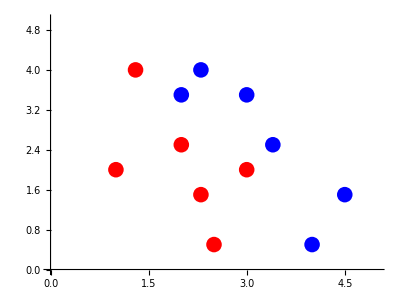

```mathematica
lplt=ListPlot[{Select[data,#⟦2⟧==-1&]⟦All,1⟧,Select[data,#⟦2⟧==1&]⟦All,1⟧},PlotMarkers->{"●",16},PlotStyle->{Blue,Red},AspectRatio->3/4,PlotRange->{{0,5},{0,5}}]
```

#### 1. Создаем набор правил

```mathematica
X=data⟦All,1⟧
y=data⟦All,2⟧
```

{{1.3,4},{1,2},{2,2.5},{2,3.5},{2.5,0.5},{2.3,1.5},{2.3,4},{3,2},{3,3.5},{4,0.5},{4.5,1.5},{3.4,2.5}}

{1,1,1,-1,1,1,-1,1,-1,-1,-1,-1}

```mathematica
xrange=Sort@DeleteDuplicates@X⟦All,1⟧
{xmin,xmax}={xrange⟦1⟧,xrange⟦-2⟧}
```

{1,1.3,2,2.3,2.5,3,3.4,4,4.5}

{1,4}

```mathematica
oxgrid=Subdivide[xmin,xmax,10]
```

{1,13/10,8/5,19/10,11/5,5/2,14/5,31/10,17/5,37/10,4}

```mathematica
Clear[GetGrid]
GetGrid[z_,size_]:=
Module[{zrange,zmin,zmax},
zrange=Sort@DeleteDuplicates@z;
{zmin,zmax}={zrange⟦1⟧,zrange⟦-2⟧};
Subdivide[zmin,zmax,size]
]
```

#### 2. Строим решающий пень

```mathematica
w0=ConstantArray[1/Length@X,Length@X]
```

{1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12}

```mathematica
mask=Thread[X⟦All,1⟧≤oxgrid⟦1⟧]
```

{False,True,False,False,False,False,False,False,False,False,False,False}

```mathematica
Pick[y,mask,True]
```

{1}

```mathematica
Pick[y,mask,False]
Commonest[Pick[y,mask,False]]
```

{1,1,-1,1,1,-1,1,-1,-1,-1,-1}

{-1}

```mathematica
yleft=First@Commonest[Pick[y,mask,True]]
yright=First@Commonest[Pick[y,mask,False]]
```

1

-1

```mathematica
pred=mask/.{True->yleft,False->yright}
y
```

{-1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

{1,1,1,-1,1,1,-1,1,-1,-1,-1,-1}

```mathematica
rule=MapThread[Unequal,{y,pred}]
```

{True,False,True,False,True,True,False,True,False,False,False,False}

```mathematica
error=Total@Pick[w0,rule]
```

5/12

```mathematica
Clear[DecisionStump]
DecisionStump[X_,y_,w0_,grid_]:=
Module[
{best={0,1},mask,yleft,yright,pred,rule,error,i},

For[i=1,i≤Length@grid,
mask=Thread[X≤grid⟦i⟧];
yleft=First@Commonest[Pick[y,mask,True]];
yright=First@Commonest[Pick[y,mask,False]];
pred=mask/.{True->yleft,False->yright};
rule=MapThread[Unequal,{y,pred}];
error=Total@Pick[w0,rule];
If[error≤best⟦2⟧,best={grid⟦i⟧,error,{yleft,yright},rule}];
i++];

best
]
```

#### 3. Повторяем построение решающих пней и меняем веса объектов

```mathematica
Clear[AdaBoost]
AdaBoost[X_,y_,OptionsPattern[{GridSize->10,Estimators->3}]]:=
Module[
{oxgrid,oygrid,w0,stumps,oxstump,oystump,dstump,o,alpha,wt,i},

oxgrid=GetGrid[X⟦All,1⟧,OptionValue[GridSize]];
oygrid=GetGrid[X⟦All,2⟧,OptionValue[GridSize]];

w0=ConstantArray[1/Length@X,Length@X];
stumps={};

For[i=1,i≤OptionValue[Estimators],
oxstump=DecisionStump[X⟦All,1⟧,y,w0,oxgrid];
oystump=DecisionStump[X⟦All,2⟧,y,w0,oygrid];
{dstump,o}=If[oxstump⟦2⟧≤oystump⟦2⟧,{oxstump,1},{oystump,2}];
alpha=1/2 Log[(1-dstump⟦2⟧)/dstump⟦2⟧];
wt=w0 Exp[-alpha*(dstump⟦4⟧/.{True->-1,False->1})];
w0=Normalize[wt,Total];
stumps=Append[stumps,{dstump⟦1⟧,o,w0}];
i++];

stumps
]
```

```mathematica
Clear[AdaVisualization]
AdaVisualization[data_,solution_,steps_,OptionsPattern[{PlotRange->{{0,5},{0,5}},Axes->{True,True}}]]:=
DynamicModule[{gr,cplt,rng},
Manipulate[
rng=OptionValue[PlotRange];
gr=Graphics[Thread[{PointSize/@(0.4solution⟦k,3⟧),data⟦All,2⟧/.{1->Red,-1->Blue},Point/@data⟦All,1⟧}],AspectRatio->3/4,PlotRange->rng,Axes->OptionValue[Axes]];
cplt=ContourPlot[If[solution⟦k,2⟧==1,x,y]==solution⟦k,1⟧,{x,rng⟦1,1⟧,rng⟦1,2⟧},{y,rng⟦2,1⟧,rng⟦2,2⟧},AspectRatio->3/4,PlotRange->rng,Axes->OptionValue[Axes]];
Show[gr,cplt],
{{k,1,"step"},1,steps,1}]
]
```

#### 4. Визуализация решения

```mathematica
sol=AdaBoost[X,y,GridSize->10,Estimators->3]
```

{{31/10,1,{1/18,1/18,1/18,1/6,1/18,1/18,1/6,1/18,1/6,1/18,1/18,1/18}},{19/10,1,{1/28,1/28,1/8,3/28,1/8,1/8,3/28,1/8,3/28,1/28,1/28,1/28}},{3.2,2,{1/8,1/48,7/96,1/16,7/96,7/96,1/16,7/96,1/16,1/8,1/8,1/8}}}

```mathematica
demo=Prepend[sol,{0,Null,w0}];
AdaVisualization[data,demo,4,Axes->False]
```

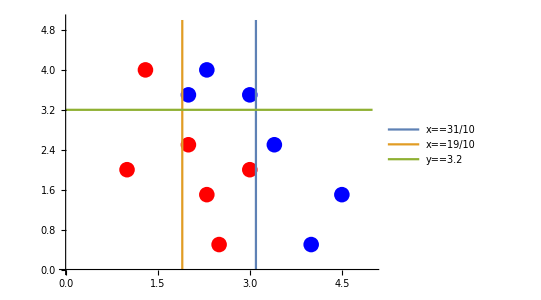

```mathematica
cplt=ContourPlot[{x==sol⟦1,1⟧,x==sol⟦2,1⟧,y==sol⟦3,1⟧},{x,0,5},{y,0,5},PlotLegends->"Expressions"];
Show[{lplt,cplt}]
```

### Модельные данные

```mathematica
SeedRandom[23]
class1=RandomVariate[NormalDistribution[2,1],{15,2}];
class2=RandomVariate[NormalDistribution[4,3],{15,2}];
```

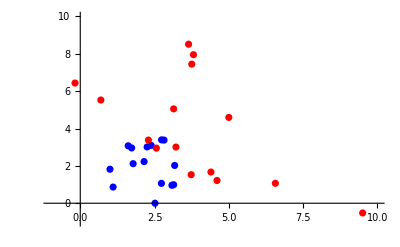

```mathematica
lplt1=ListPlot[{class1,class2},PlotStyle->{Blue,Red},PlotRange->{{-1,10},{-1,10}}]
```

```mathematica
class1=Thread[{class1,1}]
class2=Thread[{class2,-1}]
```

{{{1.72905,2.95914},1},{{3.14218,0.990182},1},{{1.10507,0.866135},1},{{3.17625,2.02211},1},{{2.81896,3.38032},1},{{2.25005,3.01357},1},{{3.08473,0.961475},1},{{1.77913,2.11764},1},{{0.999877,1.8194},1},{{2.73625,3.39236},1},{{2.73082,1.06328},1},{{2.14763,2.23026},1},{{2.51403,0.000718808},1},{{2.38697,3.09408},1},{{1.61303,3.07442},1}}

{{{2.56057,2.94993},-1},{{2.2931,3.38107},-1},{{3.14167,5.05229},-1},{{4.99885,4.59366},-1},{{4.60114,1.21596},-1},{{3.73253,1.52793},-1},{{4.39714,1.6691},-1},{{3.21976,3.00711},-1},{{0.693466,5.52612},-1},{{3.64433,8.51384},-1},{{3.80906,7.95336},-1},{{6.56396,1.06727},-1},{{-0.175774,6.43543},-1},{{9.50161,-0.520337},-1},{{3.75186,7.44729},-1}}

```mathematica
X1=Join[class1⟦All,1⟧,class2⟦All,1⟧];
y1=Join[class1⟦All,2⟧,class2⟦All,2⟧];
```

```mathematica
sol1=AdaBoost[X1,y1,GridSize->10,Estimators->5]
```

{{3.19409,1,{1/50,1/50,1/50,1/50,1/50,1/50,1/50,1/50,1/50,1/50,1/50,1/50,1/50,1/50,1/50,1/10,1/10,1/10,1/50,1/50,1/50,1/50,1/50,1/10,1/50,1/50,1/50,1/10,1/50,1/50}},{2.86914,2,{1/22,1/78,1/78,1/78,1/22,1/22,1/78,1/78,1/78,1/22,1/78,1/78,1/78,1/22,1/22,5/78,5/78,5/78,1/78,1/22,1/22,1/22,1/78,5/78,1/78,1/78,1/22,5/78,1/22,1/78}},{3.19409,1,{39/1166,1/106,1/106,1/106,39/1166,39/1166,1/106,1/106,1/106,39/1166,1/106,1/106,1/106,39/1166,39/1166,1/10,1/10,1/10,1/106,39/1166,39/1166,39/1166,1/106,1/10,1/106,1/106,39/1166,1/10,39/1166,1/106}},{1.1744,2,{39/712,11/1620,11/1620,11/712,39/712,39/712,11/1620,11/712,11/712,39/712,11/1620,11/712,11/1620,39/712,39/712,583/8100,583/8100,583/8100,11/1620,13/540,13/540,13/540,11/1620,583/8100,11/1620,11/1620,39/712,583/8100,39/712,11/1620}},{4.56388,2,{26325/641588,4895/962382,4895/962382,7425/641588,26325/641588,26325/641588,4895/962382,7425/641588,7425/641588,26325/641588,4895/962382,7425/641588,4895/962382,26325/641588,26325/641588,51887/479418,51887/479418,51887/962382,4895/962382,5785/159806,5785/159806,5785/159806,4895/479418,51887/962382,4895/962382,4895/962382,26325/319612,51887/962382,26325/319612,4895/962382}}}

```mathematica
demo1=Prepend[sol1,{0,Null,ConstantArray[1/30,30]}];
AdaVisualization[Join[class1,class2],demo1,6,PlotRange->{{-1,10},{-1,10}},Axes->True]
```

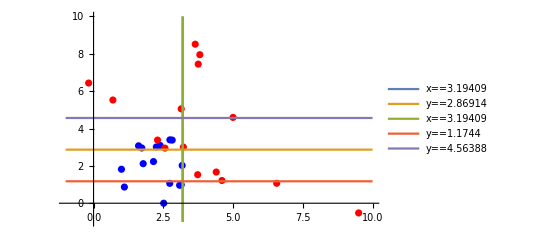

```mathematica
cplt1=ContourPlot[{x==sol1⟦1,1⟧,y==sol1⟦2,1⟧,x==sol1⟦3,1⟧,y==sol1⟦4,1⟧,y==sol1⟦5,1⟧},{x,-1,10},{y,-1,10},PlotLegends->"Expressions",PlotRange->{{-1,10},{-1,10}}];
Show[{lplt1,cplt1}]
```